```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 18];
```

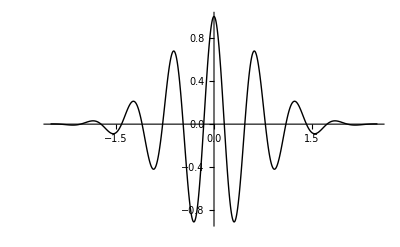

Block::lvset: Local variable specification {t = 1, ω_0 = 7} contains ω_0 = 7, which is an assignment to ω_0; only assignments to symbols are allowed.

```mathematica
Clear[e, tT, t, omega]

e[t_] := E^(-t^2/tT^2) Cos[ omega t ]

qmTwoL21Fig4 = Plot[ 
Block[{tT=1,omega=10},e[t]],{t,-2.5,2.5}, 
PlotStyle->{Thick,Black}, 
Ticks -> None]
```

```mathematica
ft[ω_] = Distribute[FullSimplify[FourierTransform[ e[t], t, ω]]]
```

(ⅇ^(-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))+(ⅇ^(omega tT^2 ω-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))

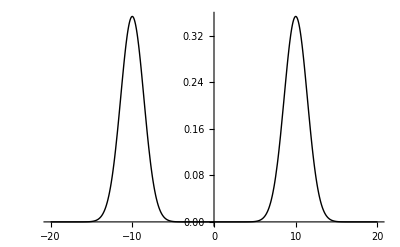

```mathematica
FTgaussianWavePacket = Plot[ Block[{tT=1,omega=10},ft[ω]],{ω,-20,20}, 
PlotStyle->{Thick, Black}]
```

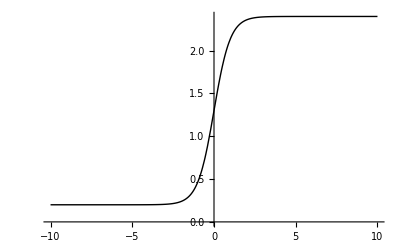

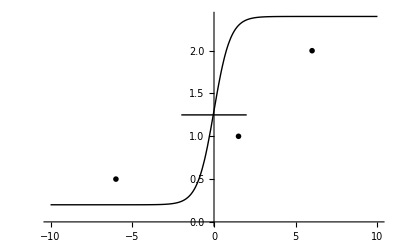

```mathematica
psuddenStepHamiltonian = Plot[1.1Tanh[x] + 1.3, {x, -10, 10}, 
PlotStyle->{Thick, Black}, 
Ticks -> None
]

suddenStepHamiltonian = Show[{
psuddenStepHamiltonian, 
Graphics[{
Thick,
Line[{{-2,1.25}, {2, 1.25}}],
Text[MaTeX["H_F"], {6, 2}],
Text[MaTeX["H_0"], {-6, 0.5}],
Text[MaTeX["\\Delta t"], {1.5, 1}]
}]}]
```

original hand markup version, no longer used:

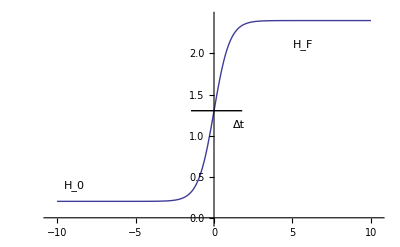

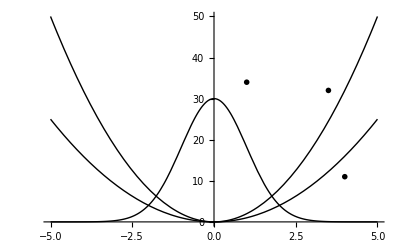

```mathematica
(*callout transparency looks bad with colored background*)
(*suddenHamiltonianPertubationHO = Show[{
Plot[
{ Callout[x^2, MaTeX["V_F"]],
 Callout[2 x^2,  MaTeX["V_0"]], 
30 E^{-x^2/2}
},
{x, -5, 5}, 
Ticks-> None,
PlotStyle->{{Thick, Black}, {Thick,Black}, {Thick, Black}}
],
Graphics[{
Text[MaTeX["\\lvert \\psi_{\\mathrm{before}} \\rangle"], {1,34}]
}]
}]*)
suddenHamiltonianPertubationHO = Show[{
Plot[
{ x^2, 
2 x^2,  
30 E^{-x^2/2}
},
{x, -5, 5}, 
Ticks-> None,
PlotStyle->{{Thick, Black}, {Thick,Black}, {Thick, Black}}
],
Graphics[{
Text[MaTeX["\\lvert \\psi_{\\mathrm{before}} \\rangle"], {1,34}],
Text[MaTeX["V_0"], {3.5, 2 4^2}],
Text[MaTeX["V_F"], {4, 4^2-5}]
}]
}]
```

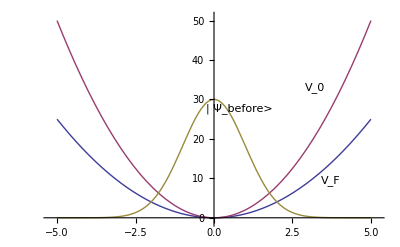

```mathematica
peeters`exportForLatex["gaussianWavePacket",qmTwoL21Fig4]
```

{gaussianWavePacket.eps,gaussianWavePacketpn.png}

```mathematica
peeters`exportForLatex["FTgaussianWavePacket",FTgaussianWavePacket]
```

{FTgaussianWavePacket.eps,FTgaussianWavePacketpn.png}

```mathematica
peeters`exportForLatex["qmTwoL21Fig4",qmTwoL21Fig4]
```

{qmTwoL21Fig4.eps,qmTwoL21Fig4pn.png}

```mathematica
peeters`exportForLatex["suddenStepHamiltonian",suddenStepHamiltonian]
```

{suddenStepHamiltonian.eps,suddenStepHamiltonianpn.png}

```mathematica
peeters`exportForLatex["suddenHamiltonianPertubationHO",suddenHamiltonianPertubationHO]
```

{suddenHamiltonianPertubationHO.eps,suddenHamiltonianPertubationHOpn.png}